{245.72,327.93,455.82,592.83,631.59,646.13,667.07,677.35,683.3,685.36,692.55,702.89,748.94,783.45,817.53,833.84,905.92,1106.9,1203.5,1245.5,1481.4,1743.8,1946.6,2066.}

{60378.3,107538.,207772.,351447.,398906.,417484.,444982.,458803.,466899.,469718.,479626.,494054.,560911.,613794.,668355.,695289.,820691.,1.22523×10^6,1.44841×10^6,1.55127×10^6,2.19455×10^6,3.04084×10^6,3.78925×10^6,4.26836×10^6}

{5490.,3656.67,1800.34,646.25,415.532,393.061,263.438,268.788,378.043,262.727,393.409,298.333,466.19,656.667,797.692,865.,1225.29,2190.,2461.59,2802.5,3656.67,4573.33,5109.05,5566.92}

{3.01401×10^7,1.33712×10^7,3.24124×10^6,417639.,172667.,154497.,69399.3,72246.9,142917.,69025.6,154771.,89002.8,217334.,431211.,636313.,748225.,1.50135×10^6,4.7961×10^6,6.05943×10^6,7.85401×10^6,1.33712×10^7,2.09154×10^7,2.61024×10^7,3.09906×10^7}

{{60378.3,3.01401×10^7},{107538.,1.33712×10^7},{207772.,3.24124×10^6},{351447.,417639.},{398906.,172667.},{417484.,154497.},{444982.,69399.3},{458803.,72246.9},{466899.,142917.},{469718.,69025.6},{479626.,154771.},{494054.,89002.8},{560911.,217334.},{613794.,431211.},{668355.,636313.},{695289.,748225.},{820691.,1.50135×10^6},{1.22523×10^6,4.7961×10^6},{1.44841×10^6,6.05943×10^6},{1.55127×10^6,7.85401×10^6},{2.19455×10^6,1.33712×10^7},{3.04084×10^6,2.09154×10^7},{3.78925×10^6,2.61024×10^7},{4.26836×10^6,3.09906×10^7}}

FittedModel[-9.14071×10^6+(2.31677×10^12)/x+9.38906 x]

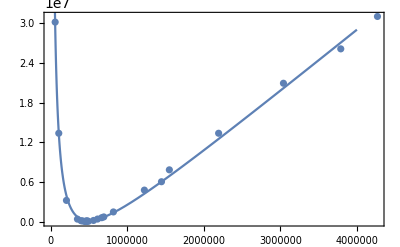
-Graphics-|Z|^2f^2

```mathematica
A={245.72,327.93,455.82,592.83,631.59,646.13,667.07,677.35,683.3,685.36,692.55,702.89,748.94,783.45,817.53,833.84,905.92,1106.9,1203.5,1245.5,1481.4,1743.8,1946.6,2066.0}

A = A^2

B={5490.0,3656.666666666667,1800.3448275862067,646.25,415.53191489361706,393.06122448979596,263.4375,268.78787878787875,378.04347826086956,262.72727272727275,393.4090909090909,298.33333333333337,466.19047619047615,656.6666666666667,797.6923076923076,865.0000000000001,1225.2941176470586,2190.0,2461.5909090909095,2802.5,3656.666666666667,4573.333333333333,5109.047619047618,5566.923076923076}

B = B^2

data=Transpose[{A,B}]
nlm=NonlinearModelFit[data,a x+b/x+c,{a,b,c},x]
Labeled[Show[ListPlot[data],Plot[nlm[x],{x,0,4000000}],Frame->True],{"|Z|^2","f^2"},{Left,Bottom},RotateLabel->False]
nlm["FitResiduals"];
ListPlot[%,Filling->Axis]
```

```mathematica
FittedModel[-8.788995357683891*^6+(2.5957385328506616*^12)/x+8.702394391400247 x]
```

FittedModel[-8.789×10^6+(2.59574×10^12)/x+8.70239 x]

```mathematica
Show[%82,ImageSize->Large]
```

```mathematica
Show[%83,AxesLabel->{HoldForm[f^2],RawBoxes[RowBox[{"|","Z",SuperscriptBox["|","2"]}]]},PlotLabel->HoldForm[Schwingkreis Fitfunktion],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%63,ImageSize->Large]
```

```mathematica
Show[%64,AxesLabel->{HoldForm[f^2],RawBoxes[RowBox[{"expression",RowBox[{RowBox[{"(",RowBox[{"paste",RowBox[{"(",RowBox[{"\"|\"",","," ","Z",","," ","\"|\""}],")"}]}],")"}],"^","2"}]}]]},PlotLabel->HoldForm[Fitfunktion Schwingkreis],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%65,ImageSize->Medium]
```

```mathematica
Show[%66,ImageSize->Large]
```

```mathematica
Show[%67,AxesLabel->{HoldForm[TEST],RawBoxes[RowBox[{"expression",RowBox[{RowBox[{"(",RowBox[{"paste",RowBox[{"(",RowBox[{"\"|\"",","," ","Z",","," ","\"|\""}],")"}]}],")"}],"^","2"}]}]]},PlotLabel->None]
```